#### Init

```mathematica
$HistoryLength=5;
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/home/matt/datadrop/Dropbox/Berman-Research/cluster/diss/calcs

```mathematica
Import["../D-params.m"]
```

```mathematica
Import["../D-nde-funcs.m"]
```

```mathematica
Import["../D-gen-funcs.m"]
```

```mathematica
Import["../D-clus-funcs.m"]
```

```mathematica
ResourceFunction["KernelStatusGrid"];
```

```mathematica
CreatePalette[
Column[
{
ResourceFunction["KernelStatusGrid"][],
Button["Update clus-funcs",Import["../D-clus-funcs.m"]],
Dynamic[Refresh[bgb@MemoryInUse[],UpdateInterval->1]](*,
Style[Dynamic[Refresh[#,UpdateInterval->1]]&/@{mugb,bgb[MaxMemoryUsed[]]},24,Black]*)
},
Center
]
];
```

```mathematica
dfd="../../../dis/figs/";
lc1d="lc-1dp-v1/";
p1d="cl-1dp-v1/";
p1drp="lc-1dp-v1-reproc/";
p2d="cl-2dp-v1/";
c2d="cl-2dc-v1/";
c2d2="cl-2dc-v2/";
```

```mathematica
AbsoluteTiming[fl2d=Import[c2d2<>"all-kap-1-ds.m"];]
```

{0.770192,Null}

# Use these functions for ref comments on DMPE?

## Plot DPME integrands

#### Already made a function to import a ton of EFs, so just go with that

```mathematica
LightYellow~bg~bgb@MemoryInUse[]
AbsoluteTiming[allmx=Normal@fl2d[
Values/*1,
Values,
"nefs"/*Import
];]
allmx//Dimensions
allmx[[1,1]]
bgb@ByteCount[allmx]
LightRed~bg~bgb@MemoryInUse[]
allmxevs=Normal@fl2d[Values/*1,Values,"evs"/*Values/*Abs];
Dimensions@allmxevs
allmxmx=Normal@fl2d[Values/*1,Values,"mx"];
%//Dimensions
```

```mathematica
allmx[[1,1]][0,0]
```

-0.0197937

### How to plot?

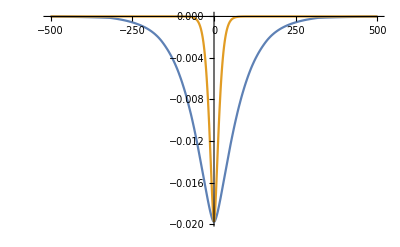

```mathematica
Plot[
{
allmx[[1,1]][x,0],
allmx[[1,1]][0,x]
},
{x,-500,500},
AxesOrigin->{0,0},
PlotRange->All
]
```

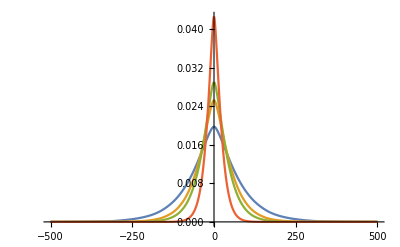

```mathematica
Plot[
{
Abs@Re@allmx[[1,1]][x,0],
Abs@Re@allmx[[2,1]][x,0],
Abs@Re@allmx[[3,1]][x,0],
Abs@Re@allmx[[10,1]][x,0]
},
{x,-500,500},
AxesOrigin->{0,0},
PlotRange->All
]
```

```mathematica
Dimensions@allmx
```

{37,12}

```mathematica
Table[0.005*(i-1),{i,10}]
```

{0.,0.005,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045}

#### Seriously, what the fuck is this shit

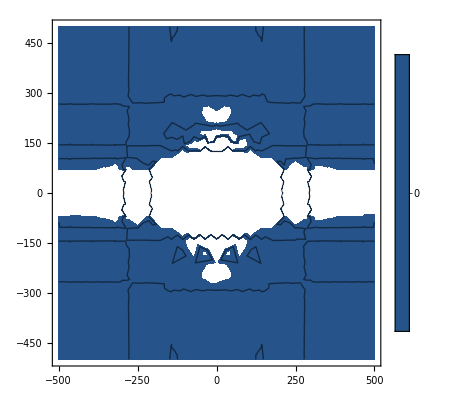

```mathematica
ContourPlot[
allmx[[10,1]][x,y],
{x,-500,500},{y,-500,500},
PlotTheme->"Detailed",
Contours->Table[0.001*(i-1),{i,100}]
]
```

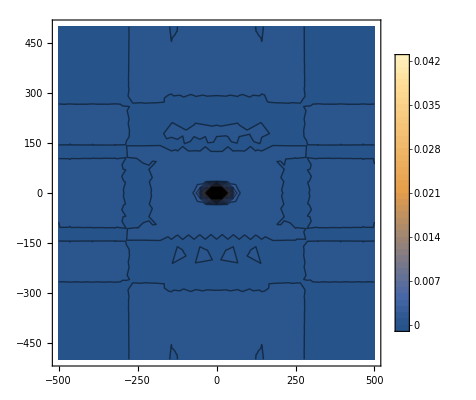

```mathematica
ContourPlot[
allmx[[10,1]][x,y],
{x,-500,500},{y,-500,500},
PlotTheme->"Detailed",
PlotRange->All,
Contours->Table[0.001*(i-1),{i,100}]
]
```

```mathematica
ContourPlot[
allmx[[10,1]][x,y],
{x,-500,500},{y,-500,500},
PlotTheme->"Detailed",
PlotRange->Full,
Contours->Table[0.001*(i-1),{i,100}]
]
```

-Graphics-

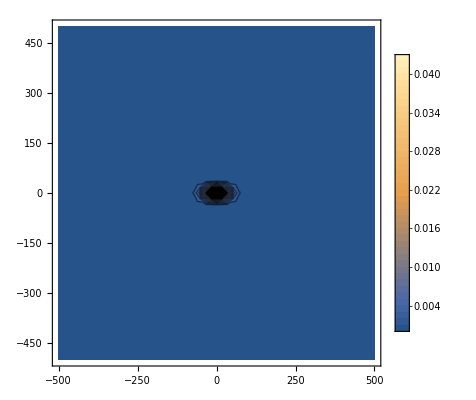

```mathematica
ContourPlot[
allmx[[10,1]][x,y],
{x,-500,500},{y,-500,500},
PlotTheme->"Detailed",
PlotRange->All,
Contours->Table[0.001*(i),{i,100}]
]
```

#### Plot3D?

```mathematica
Plot3D[
allmx[[10,1]][x,y],
{x,-500,500},{y,-500,500},
PlotTheme->"Detailed",
PlotRange->Full
]
```

-Graphics3D-

### Manipulate, Table, and Block

```mathematica
ContourPlot[
allmx[[10,1]][x,y],
{x,-500,500},{y,-500,500},
PlotTheme->"Detailed",
PlotRange->{Automatic,Automatic,Automatic},
Contours->Table[0.001*(i-1),{i,100}]
]
```

-Graphics-

```mathematica
Manipulate[
Show[
polt,
ColorFunction->"BlueGreenYellow",
PlotRange->{{-xv,xv},{-yv,yv},Full}
],
{xv,50,500},{yv,50,500},
Initialization:>(polt=ContourPlot[allmx[[5,1]][x,y],{x,-1000,1000},{y,-1000,1000},Contours->Table[0.001*(i-1),{i,100}],PlotTheme->"Detailed"]),
SynchronousInitialization->False
]
```

OptionValue::nodef: Unknown option ColorFunction for Graphics.

## Compare ratios of the x/y E_tr, f-bars, and (f-bar / E_tr) -

Etrx > Etry by about 2.5x.
	fbx > fby by about 27x
	dpmex > dpmey by 10x

```mathematica
(*TableForm@Normal@*)fl2d[1,Values,
{
"etr"/*KeyDrop["j1"]/*(QuantityMagnitude[#,"Hartrees"]&),
"fbx"/*"i1",
"fby"/*"i1"
}
/*
Values/*(Flatten[#,{{2},{1}}]&)
/*
(<|
"etfbx"->SelectFirst[Re[#[[2]]]>10^-4&]/*(#[[{1,2}]]&),
"etfby"->SelectFirst[Re[#[[3]]]>10^-4&]/*(#[[{1,3}]]&)
|>)
/*
(Module[
{etrx=#etfbx[[1]],fbx=#etfbx[[2]],etry=#etfby[[1]],fby=#etfby[[2]]},
<|
"etfbx"->{etrx,fbx},
"etdpx"->{etrx,(fbx/etrx)},
"etfby"->{etry,fby},
"etdpy"->{etry,(fby/etry)},
"detr"->etrx/etry,
"dfb"->fbx/fby,
"ddp"->(fbx/etrx)/(fby/etry)
|>
]&)
]
```

Dataset[<>]

#### Experimenting

```mathematica
fl2d[Keys]
```

Dataset[<>]

```mathematica
fl2d[1,Keys]
```

Dataset[<>]

```mathematica
fl2d[1,1,Keys]
```

Dataset[<>]

```mathematica
fl2d[
1,Values,
{
"fbx"/*1/*SelectFirst[Re[#]>10^-4&],
"fby"/*1/*SelectFirst[Re[#]>10^-4&]
}
]
```

Dataset[<>]

```mathematica
fl2d[1,1,"etr"]
```

Dataset[<>]

```mathematica
Normal@fl2d[1,1,
{
{
"etr"/*KeyDrop["j1"]/*(QuantityMagnitude[#,"Hartrees"]&),
"fbx"/*"i1"
},
{
"etr"/*KeyDrop["j1"]/*(QuantityMagnitude[#,"Hartrees"]&),
"fby"/*"i1"
}
}
/*
Values
/*
(
Flatten[
#,
{{2},{1}}
]&)
]
```

{{{0.00508716,0.00725667,0.00892479,0.00999869,0.0109055,0.011551,0.0121431,0.0125682,0.0127741,0.0129218,0.0133692},{0.00508716,0.00725667,0.00892479,0.00999869,0.0109055,0.011551,0.0121431,0.0125682,0.0127741,0.0129218,0.0133692}},{{9.18002×10^-19,2.45514×10^-22,6.14973×10^-20,1.51398×10^-19,5.0687×10^-17,1.5533×10^-17,1.31853×10^-17,1.73253×10^-17,35.0575,1.30196×10^-14,9.81905×10^-8},{1.30187,4.03722×10^-20,0.0676449,4.21489×10^-17,0.0177011,7.97384×10^-18,0.00764196,1.2928×10^-18,3.48139×10^-20,0.00309295,5.7646×10^-12}}}

```mathematica
Normal@fl2d[1,1,
{
"etr"/*KeyDrop["j1"]/*(QuantityMagnitude[#,"Hartrees"]&),
"fbx"/*"i1",
"fby"/*"i1"
}
/*
Values/*(Flatten[#,{{2},{1}}]&)
/*
(<|
"bex"->SelectFirst[Re[#[[2]]]>10^-4&]/*(#[[{1,2}]]&),
"bey"->SelectFirst[Re[#[[3]]]>10^-4&]/*(#[[{1,3}]]&)
|>)
(*/*
(<|
"fbx"->,
"dpx"->,
"fby"->,
"dpy"->
|>)*)
]
```

<|bex→{0.0127741,35.0575},bey→{0.00508716,1.30187}|>

```mathematica
(*Normal@*)fl2d[1,1;;5,
{
"etr"/*KeyDrop["j1"]/*(QuantityMagnitude[#,"Hartrees"]&),
"fbx"/*"i1",
"fby"/*"i1"
}
/*
Values/*(Flatten[#,{{2},{1}}]&)
/*
(<|
"etfbx"->SelectFirst[Re[#[[2]]]>10^-4&]/*(#[[{1,2}]]&),
"etfby"->SelectFirst[Re[#[[3]]]>10^-4&]/*(#[[{1,3}]]&)
|>)
/*
(Module[
{etrx=#etfbx[[1]],fbx=#etfbx[[2]],etry=#etfby[[1]],fby=#etfby[[2]]},
<|
"etfbx"->{etrx,fbx},
"etdpx"->{etrx,(fbx/etrx)},
"etfby"->{etry,fby},
"etdpy"->{etry,(fby/etry)}
|>
]&)
]
```

Dataset[<>]

```mathematica
Normal@fl2d[1,1,
{
"etr"/*KeyDrop["j1"]/*(QuantityMagnitude[#,"Hartrees"]&),
"fbx"/*"i1",
"fby"/*"i1"
}
/*
Values/*(Flatten[#,{{2},{1}}]&)
/*
(<|
"fbx"->SelectFirst[Re[#[[2]]]>10^-4&]/*2,
"fby"->SelectFirst[Re[#[[3]]]>10^-4&]/*3
|>)
/*
(<|
"fbx"->,
"dpx"->,
"fby"->,
"dpy"->
|>)
]
```

# 2DC v2.1

## Done (as of 08/05):

## All EVs

### 08/07: Try re-sizing Figs. 7.1 & 7.2 so they are more readable and take up less space.

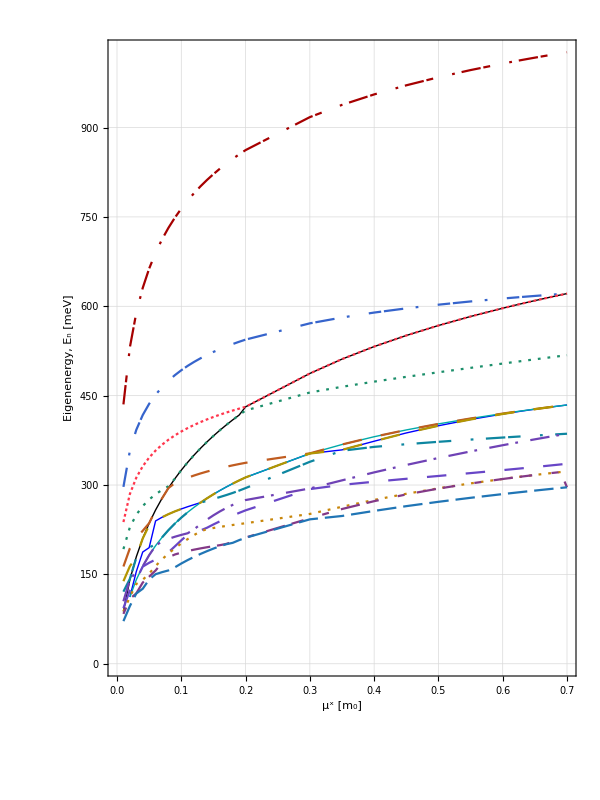
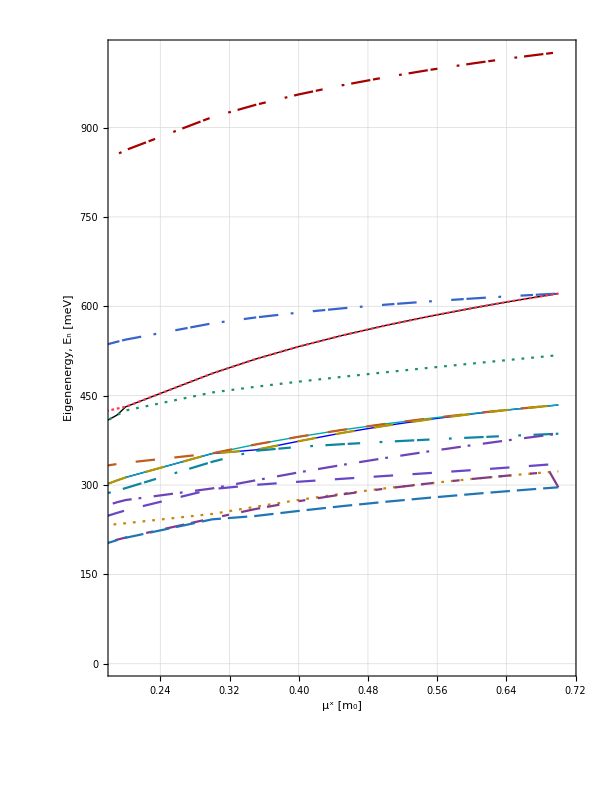
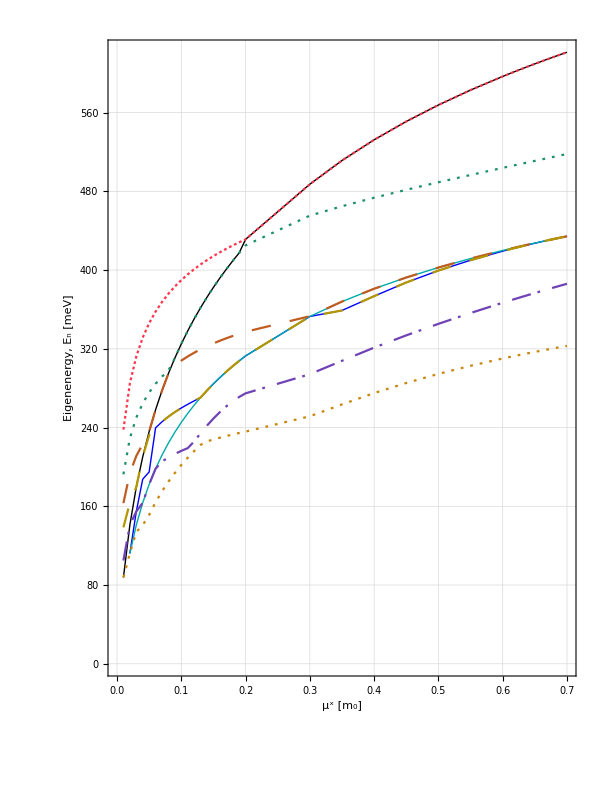
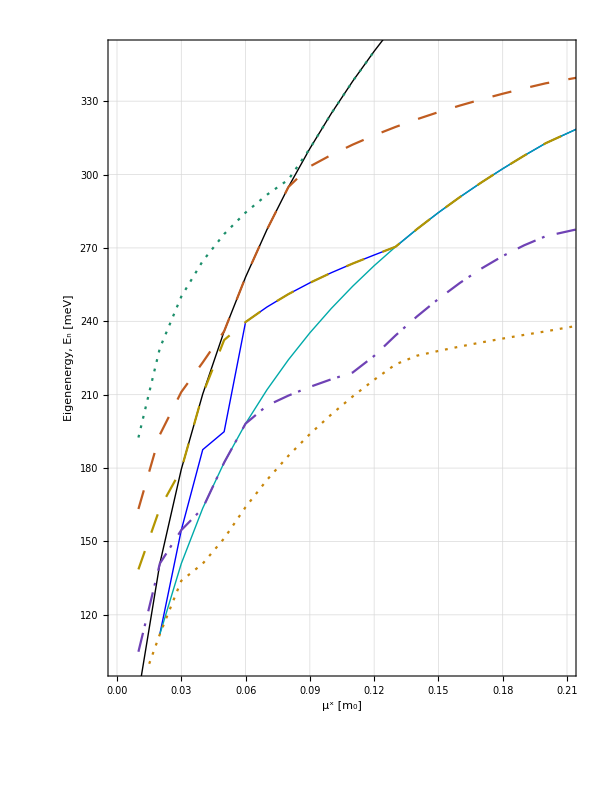

```mathematica
Normal@fl2d[
1,
Values
/*
(Module[
{flatdata=Flatten[#,{{3},{1},{2}}]},
Map[
ListLinePlot[
#data,
PlotTheme->"Detailed",
ImageSize->{600,800},AspectRatio->Full,
PlotRange->#plra,
FrameLabel->{{"Eigenenergy, E_n [meV]",None},{"μ^x [m_0]",None}},
LabelStyle->labsty/.{24->22},
PlotStyle->#plst,
(*PlotMarkers->marksize[Flatten[{emmarks4,"△","▽"}],24],*)
PlotLegends->None,
Prolog->{
{Black,Thick,Line[Flatten[{{flatdata[[10,1]]},{flatdata[[8,2]]},flatdata[[6,3;;4]],flatdata[[5,5;;8]],flatdata[[4,9;;19]],flatdata[[3,20;;]]},1]]},
{Blue,Line[Flatten[{{flatdata[[10,2]]},{flatdata[[8,3]]},flatdata[[7,4;;5]],flatdata[[6,6;;12]],flatdata[[6,13;;20]],flatdata[[6,21;;]]},1]]},
{Darker@Cyan,Line[Flatten[{{flatdata[[10,2]]},{flatdata[[9,3]]},flatdata[[8,4;;6]],flatdata[[7,7;;12]],flatdata[[6,13;;21]],flatdata[[5,22;;]]},1]]}
}
]&,
{
<|"data"->flatdata,"plra"->Full,"plst"->randash|>,
<|"data"->flatdata,"plra"->{{0.19,0.71},Automatic},"plst"->randash|>,
<|"data"->flatdata[[{3,4,5,6,8,10}]],"plra"->Full,"plst"->randash[[{3,4,5,6,8,10}]]|>,
<|"data"->flatdata[[{4,5,6,8,10}]],"plra"->{{0,0.21},{100,350}},"plst"->randash[[{4,5,6,8,10}]]|>
}
]
]&),
{
"mx"/*(Table[#,{12}]&),
"evs"/*Values/*Abs/*QuantityMagnitude
}
]
```

#### Tracing the n_x states

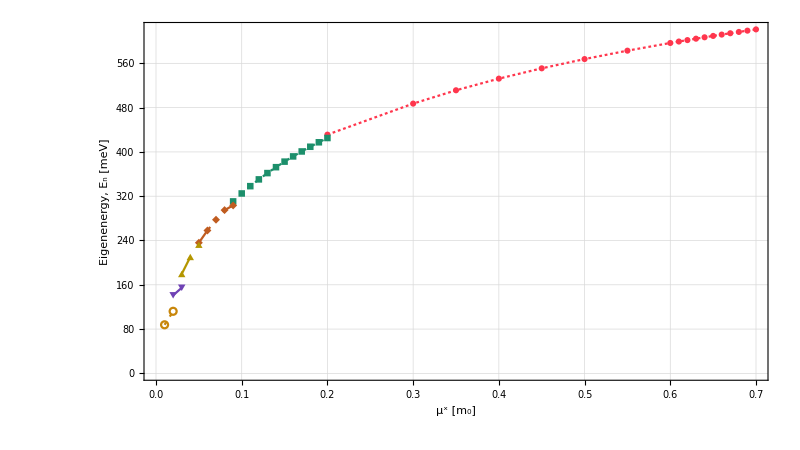

```mathematica
Normal@fl2d[
1,
Values
/*
(Module[
{allflatdata=Flatten[#,{{3},{1},{2}}]},
ListLinePlot[
{
allflatdata[[3,20;;]],
allflatdata[[4,9;;20]],
allflatdata[[5,5;;9]],
allflatdata[[6,3;;5]],
allflatdata[[8,2;;3]],
allflatdata[[10,1;;2]]
},
PlotTheme->"Detailed",ImageSize->0.5*{1600,900},AspectRatio->Full,
FrameLabel->{{"Eigenenergy, E_n [meV]",None},{"μ^x [m_0]",None}},LabelStyle->labsty,
PlotStyle->randash[[{3,4,5,6,8,10}]],
PlotRange->Full,
PlotMarkers->Automatic,
PlotLegends->Placed[PointLegend[
Automatic,
Table[TraditionalForm@StringForm["E_(`1`)",ToString@i],{i,12}],
LegendLayout->(TableForm[
Map[
Row,
Transpose@ArrayReshape[#,{6,2,2}],
{2}
]
]&)
],Above]
]
]&),
{
"mx"/*(Table[#,{12}]&),
"evs"/*Values/*Abs/*QuantityMagnitude
}
]
```

### Figs. 8.1 & 8.2 in Diss (as of 08/05): EVs vs. μ^x

#### Fig. 8.1 (All EVs)

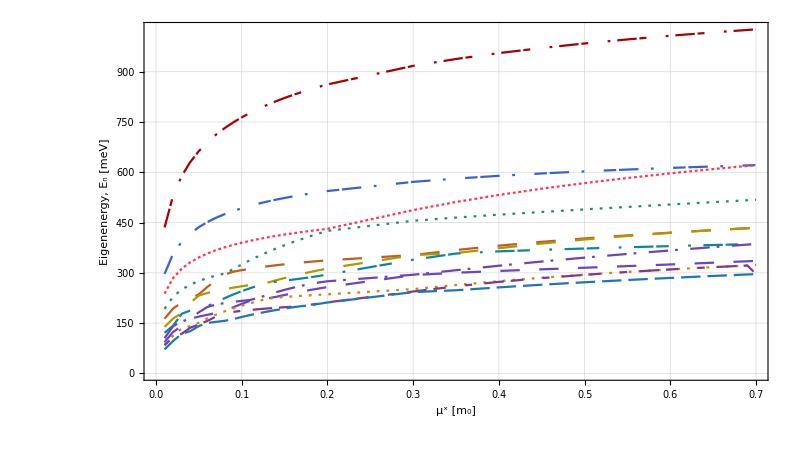

../../../dis/figs/d_leg_all-en-vs-mx_my-07.pdf

```mathematica
Normal@fl2d[
1,
Values
/*
(ListLinePlot[
Flatten[#,{{3},{1},{2}}],
PlotTheme->"Detailed",ImageSize->0.5*{1600,900},AspectRatio->Full,(*PlotLabel->"All eigenenergies vs. μ^x; μ^y = 0.7 m_0",*)FrameLabel->{{"Eigenenergy, E_n [meV]",None},{"μ^x [m_0]",None}},LabelStyle->labsty,
PlotStyle->randash,
(*PlotMarkers->marksize[Flatten[{emmarks4,"△","▽"}],24],*)
PlotLegends->Placed[LineLegend[
Automatic,
Table[TraditionalForm@StringForm["E_(`1`)",ToString@i],{i,12}],
LegendLayout->(TableForm[
Map[
Row,
Transpose@ArrayReshape[#,{6,2,2}],
{2}
]
]&)
],Above]
]&),
{
"mx"/*(Table[#,{12}]&),
"evs"/*Values/*Abs/*QuantityMagnitude
}
]
Export[dfd<>"d_leg_all-en-vs-mx_my-07.pdf",%[[2,1]]]
```

#### Fig. 8.2 (Zoomed on lower EVs)

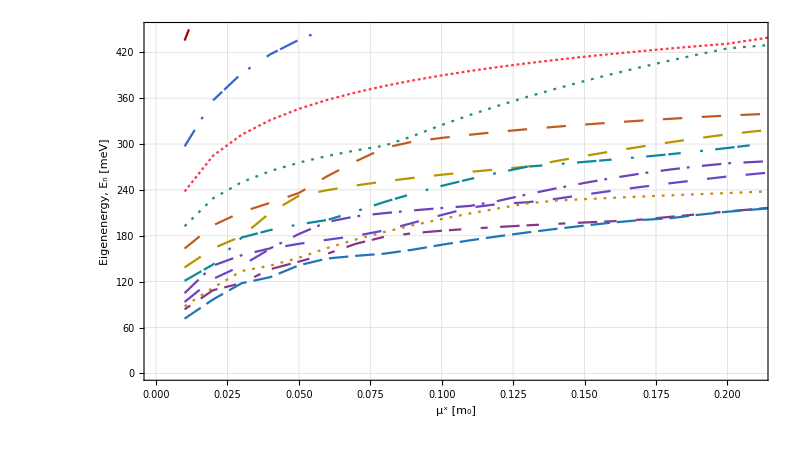

```mathematica
Normal@fl2d[
1,
Values
/*
(ListLinePlot[
Flatten[#,{{3},{1},{2}}],
PlotTheme->"Detailed",ImageSize->0.5*{1600,900},AspectRatio->Full,
FrameLabel->{{"Eigenenergy, E_n [meV]",None},{"μ^x [m_0]",None}},LabelStyle->labsty,
PlotStyle->randash,
PlotRange->{{0,0.21},{0,450}},
PlotLegends->Placed[PointLegend[
Automatic,
Table[TraditionalForm@StringForm["E_(`1`)",ToString@i],{i,12}],
LegendLayout->(TableForm[
Map[
Row,
Transpose@ArrayReshape[#,{6,2,2}],
{2}
]
]&)
],Above]
]&),
{
"mx"/*(Table[#,{12}]&),
"evs"/*Values/*Abs/*QuantityMagnitude
}
]
```

### E_b vs. μ^(x/y) and μ^0 (ContourPlot)

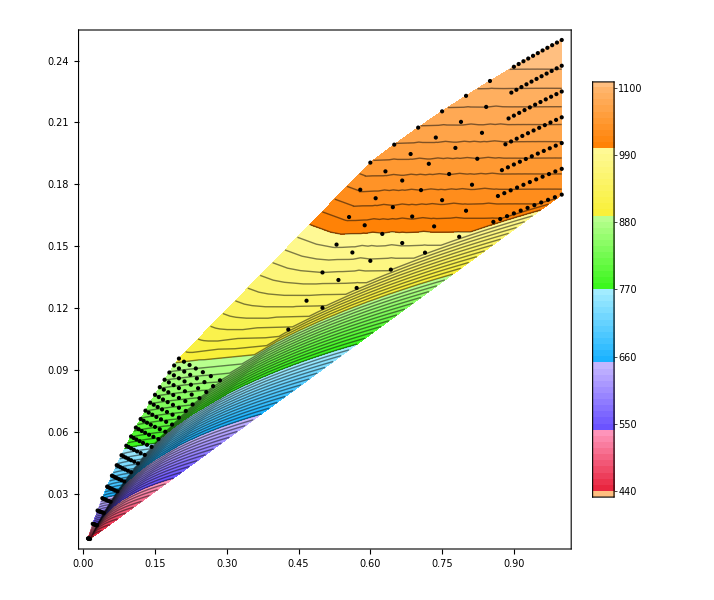

```mathematica
fl2d[
Values
/*
(ListContourPlot[
Flatten[#,1],
ImageSize->0.5*{1200,1200},
PlotTheme->"Detailed",
ColorFunction->"BrightBands",
Contours->Table[400+10*i,{i,0,70}],
Epilog->{
{Black,Point[Flatten[#,1][[;;,;;2]]]}
}
]&),
Values,
{
"mxy",
"m0",
"evs"/*"i1"/*Abs/*QuantityMagnitude
}
]
```

## Array Plots (for optical selection rules)

### Fun with manipulate!

```mathematica
Normal@fl2d[
1,
Values,
{
"fox"/*Values/*Map[Values],
"foy"/*Values/*Map[Values],
{"mx","my"},
"evs"/*Values
}
/*
(Module[{data=#[[;;2]],evs=#[[4]],params=#[[3]]},
ArrayPlot[
Chop[PadLeft[Subtract@@data,{11,12},"-"],10^-5],
PlotTheme->"Detailed",
ColorRules->{"-"->Gray,0->White,x_/;x>0->Lighter@Red,x_/;x<0->Darker@Blue},
PlotLegends->Placed[SwatchLegend[
{Lighter@Red,Darker@Blue},
{"f_(i → f)^x","f_(i → f)^y"},
LegendMarkerSize->30,
LabelStyle->{Black,30,FontFamily->"Arial"},
LegendFunction->(Framed[#,RoundingRadius->5]&)
],
Above
],
ImageSize->{800,800},
PlotLabel->TraditionalForm@StringForm["μ^x=`1`, μ^y=`2`",params[[1]],params[[2]]],
PlotRange->{{1,12},{1,12}},
Mesh->True,
MeshStyle->Black,
DataReversed->{False,False},
Frame->True,
FrameTicks->MapAt[
Partition[Riffle[#,evs],2]&,
Transpose@Table[{i,i,i,i},{i,12}],
{3}
],
LabelStyle->labsty,
FrameLabel->{{"Final Eigenstate, SubscriptBox[StyleBox[\"n\",FontSlant->\"Italic\"], \"f\"]",None},{"Initial Eigenstate, SubscriptBox[StyleBox[\"n\",FontSlant->\"Italic\"], \"i\"]",None}}
]]&)
];
Manipulate[
%[[i]],
{i,1,37,1}
]
```

### Saving (a) figure(s) is tricky because just one of these plots doesn’t tell the whole story.

#### Make a grid of these plots at different values of μ^x corresponding to the “anti-crossing” points (Diss fig. 08/01)

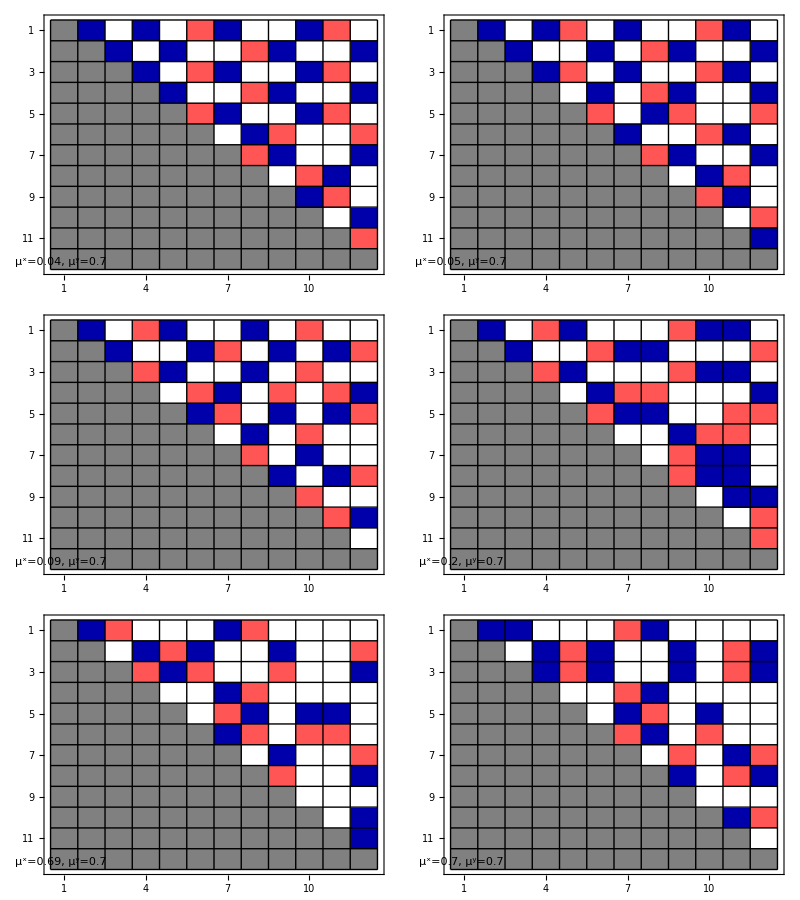
-Graphics-Initial Eigenstate, n_iFinal Eigenstate, n_fEigenenergy, E_n [meV]

../../../dis/figs/d_plt-grid_arrplt-mx-prog_my-07.pdf

```mathematica
Labeled[Grid[ArrayReshape[
Normal@fl2d[
1,
{4,5,9,20,-2,-1}/*Values,
{
"fox"/*Values/*Map[Values]/*Append[{}],
"foy"/*Values/*Map[Values]/*Append[{}],
{"mx","my"},
"evs"/*Values/*Abs/*QuantityMagnitude
}
/*
(Module[{data=#[[;;2]],evs=Map[NumberForm[#,{5,1}]&,#[[4]]],params=#[[3]]},
ArrayPlot[
Chop[PadLeft[Subtract@@data,{12,12},"-"],10^-5],
PlotTheme->"Detailed",
ColorRules->{"-"->Gray,0->White,x_/;x>0->Lighter@Red,x_/;x<0->Darker@Blue},
PlotLegends->None(*Placed[SwatchLegend[
{Lighter@Red,Darker@Blue},
{"f_(i → f)^x","f_(i → f)^y"},
LegendMarkerSize->30,
LabelStyle->{Black,30,FontFamily->"Arial"},
LegendFunction->(Framed[#,RoundingRadius->5]&)
],
Above
]*),
ImageSize->{800,800},
(*PlotLabel->TraditionalForm@StringForm["μ^x=`1`, μ^y=`2`",params[[1]],params[[2]]],*)
PlotRange->{{1,12},{1,12}},
Mesh->True,
MeshStyle->Black,
DataReversed->{False,False},
Frame->True,
FrameTicks->MapAt[
Partition[Riffle[#,evs],2]&,
Transpose@Table[{i,i,i,i},{i,12}],
{3}
],
LabelStyle->labsty/.{24->32},
Epilog->{
Inset[Framed[
Style[TraditionalForm@StringForm["μ^x=`1`, μ^y=`2`",params[[1]],params[[2]]],labsty/.{24->32}],
Background->White,RoundingRadius->5],Scaled@{0.05,0.05},Scaled@{0.05,0.05}]
}(*,
FrameLabel->{{"Final Eigenstate, SubscriptBox[StyleBox[\"n\",FontSlant->\"Italic\"], \"f\"]",None},{"Initial Eigenstate, SubscriptBox[StyleBox[\"n\",FontSlant->\"Italic\"], \"i\"]","Eigenenergy, E_n_i [meV]"}}*)
]]&)
],
{3,2}
],
Spacings->5
],
{Rotate["Initial Eigenstate, n_i",90Degree],"Final Eigenstate, n_f",Rotate["Eigenenergy, E_n [meV]",-90Degree]},{Left,Bottom,Right},LabelStyle->Directive[50,Black,FontFamily->"Arial"]]
Export[dfd<>"d_plt-grid_arrplt-mx-prog_my-07.pdf",%]
```

## 3D Plots of {E_tr,f_0,μ^x}

### Set of 6 ListPointPlot3D[]’s in Dissertation (as of 08/05)

```mathematica
etrfoxymx3d=fl2d[
Values
/*
(Flatten[#,{{3},{1},{2,4},{5}}]&)
/*
(Module[
{xdata=#[[1]],ydata=#[[2]]},
Column[
{
PointLegend[
{Blue,Magenta,Green,Red,Cyan,Orange,Purple},
Table[StringForm["μ^y=`1`",TraditionalForm@my],{my,{0.7,0.75,0.8,0.85,0.9,0.95,1.}}],
LegendMarkerSize->36,
LabelStyle->labsty/.{24->18},
LegendLayout->{"Row",1}
],
PointLegend[
{Lighter@Gray,Darker@Gray,Gray},
{"μ^x ≠ μ^y ; f_0^x","μ^x ≠ μ^y ; f_0^y","μ^x = μ^y ; f_0^(x + y)"},
LegendMarkerSize->36,
LabelStyle->labsty/.{24->18},
LegendLayout->{"Row",1}
],
TableForm[
Transpose@ArrayReshape[
Map[
ListPointPlot3D[
Flatten[
Table[
{
xdata[[i,;;-2]],
ydata[[i,;;-2]],
{{
xdata[[i,-1,1]],
xdata[[i,-1,2]]+ydata[[i,-1,2]],
xdata[[i,-1,3]]
}}
},
{i,Length[xdata]}
],
1],
FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},
ImageSize->0.5*{900,900},AspectRatio->Full,
Filling->Axis,FillingStyle->Thick,
Boxed->False,
LabelStyle->labsty,
PlotStyle->Flatten[
Table[
{AbsolutePointSize[i[[2]]],lida[col,i[[1]]]},
{col,{Blue,Magenta,Green,Red,Cyan,Orange,Purple}},
{i,{{0.3,6},{0.7,6},{0.5,10}}}
],
1],
AxesStyle->{Red,Blue,Purple},
AxesLabel->#axla,
AxesEdge->{{-1,-1},{-1,-1},{-1,1}},
Ticks->#axti,
ViewPoint->#vp,
Epilog->{
Inset[
Framed[
Style[#subfig,labsty/.{24->16}],
Background->White,RoundingRadius->5
],
Scaled@{0.99,0.99},Scaled@{0.99,0.99}
]
}
]&,
{
<|"vp"->{-2,0,2},"axla"->{" E_tr^j "," f_0^j "," μ^x "},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(f)"|>,
<|"vp"->{-Infinity,-Infinity,Infinity},"axla"->{" E_tr^j "," f_0^j "," μ^x "},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(a)"|>,
<|"vp"->{0,-2,2},"axla"->{" E_tr^j "," f_0^j "," μ^x "},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(d)"|>,
<|"vp"->{-Infinity,0,0},"axla"->{None," f_0^j "," μ^x "},"axti"->{None,Automatic,Automatic},"subfig"->"(e)"|>,
<|"vp"->{0,0,Infinity},"axla"->{" E_tr^j "," f_0^j ",None},"axti"->{Automatic,Automatic,None},"subfig"->"(b)"|>,
<|"vp"->{0,-Infinity,0},"axla"->{" E_tr^j ",None," μ^x "},"axti"->{Automatic,None,Automatic},"subfig"->"(c)"|>
},
{1}
],
{3,2}]]
},
Center]
]&),
Values,
{
"mx",
"etr"/*(2;;)/*Values,
"fox"/*1/*Values,
"foy"/*1/*Values
}
/*
(Module[
{mx=#[[1]],etr=#[[2]],fox=#[[3]],foy=#[[4]]},
{
Transpose[{etr,fox,Table[mx,{11}]}],
Transpose[{etr,foy,Table[mx,{11}]}]
}
]&)
/*Map[AssociationThread[Table[tssf["j`1`",i],{i,2,12}],#]&]
/*Map[Select[#,Abs[#[[2]]]>10^-4&,1]&]/*Values
]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
etrfoxymx3d[[1,;;-2]]
etrfoxymx3d[[1,-1,1,;;,;;]]
```

{,}

{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}}

```mathematica
{
Export[dfd<>"d_comb-3d-grid_etr-foxy-mx_new-leg.pdf",#],
Export[dfd<>"d_leg-3d-grid_etr-foxy-mx_new-leg.pdf",Column[#[[1,;;-2]],Center]],
Export[dfd<>"d_plt-3d-grid_etr-foxy-mx_new-leg.pdf",#[[1,-1]]]
}&[etrfoxymx3d]
```

{../../../dis/figs/d_comb-3d-grid_etr-foxy-mx_new-leg.pdf,../../../dis/figs/d_leg-3d-grid_etr-foxy-mx_new-leg.pdf,../../../dis/figs/d_plt-3d-grid_etr-foxy-mx_new-leg.pdf}

Save each figure individually

```mathematica
{
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-f0-side.pdf",#[[1,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_f0-above.pdf",#[[1,1]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_f0-vs-etr-side.pdf",#[[2,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-iso-perspect.pdf",#[[2,1]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-etr-side.pdf",#[[3,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_etr-above.pdf",#[[3,1]]]
}&@etrfoxymx3d[[1,-1,1]]
```

$Aborted

```mathematica
CreatePalette[Dynamic[etrfoxymx3d],WindowMargins->Automatic]
```

### Same, for (f̃)_0^j

```mathematica
etrbarfoxymx3d=fl2d[
Values
/*
(Flatten[#,{{3},{1},{2,4},{5}}]&)
/*
(Module[
{xdata=#[[1]],ydata=#[[2]]},
Column[
{
PointLegend[
{Blue,Magenta,Green,Red,Cyan,Orange,Purple},
Table[StringForm["μ^y=`1`",TraditionalForm@my],{my,{0.7,0.75,0.8,0.85,0.9,0.95,1.}}],
LegendMarkerSize->36,
LabelStyle->labsty/.{24->18},
LegendLayout->{"Row",1}
],
PointLegend[
{Lighter@Gray,Darker@Gray,Gray},
{"μ^x ≠ μ^y ; f_0^x","μ^x ≠ μ^y ; f_0^y","μ^x = μ^y ; f_0^(x + y)"},
LegendMarkerSize->36,
LabelStyle->labsty/.{24->18},
LegendLayout->{"Row",1}
],
TableForm[
ArrayReshape[
Map[
ListPointPlot3D[
Flatten[
Table[
{
xdata[[i,;;-2]],
ydata[[i,;;-2]],
{{
xdata[[i,-1,1]],
xdata[[i,-1,2]]+ydata[[i,-1,2]],
xdata[[i,-1,3]]
}}
},
{i,Length[xdata]}
],
1],
FaceGrids->#faces,
ImageSize->0.5*{900,900},AspectRatio->Full,
Filling->Axis,FillingStyle->Thick,
Boxed->False,BoxRatios->{1,1,1},
LabelStyle->labsty,
ScalingFunctions->{None,"Log",None},
PlotStyle->Flatten[
Table[
{AbsolutePointSize[i[[2]]],lida[col,i[[1]]]},
{col,{Blue,Magenta,Green,Red,Cyan,Orange,Purple}},
{i,{{0.3,6},{0.7,6},{0.5,10}}}
],
1],
AxesStyle->{Red,Blue,Purple},
AxesLabel->#axla,
AxesEdge->#axed,
Ticks->#axti,
ViewPoint->#vp,
Epilog->{
Inset[
Framed[
Style[#subfig,labsty/.{24->16}],
Background->White,RoundingRadius->5
],
Scaled@#epiloc,Scaled@#epiloc
]
}
]&,
{
<|"vp"->{-Infinity,Infinity,Infinity},"axla"->{" E_tr^j "," (f̃)_0^j "," μ^x "},"axed"->{{1,-1},{-1,-1},{1,1}},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(a)","epiloc"->{0.99,0.99},"faces"->{{0,0,-1},{0,-1,0},{1,0,0}}|>,
<|"vp"->{0,0,Infinity},"axla"->{" E_tr^j "," (f̃)_0^j ",None},"axed"->{{-1,-1},{-1,-1},{-1,1}},"axti"->{Automatic,Automatic,None},"subfig"->"(b)","epiloc"->{0.99,0.99},"faces"->{{0,0,-1},{0,1,0},{1,0,0}}|>,
<|"vp"->{0,-Infinity,0},"axla"->{" E_tr^j ",None," μ^x "},"axed"->{{-1,-1},{-1,-1},{-1,1}},"axti"->{Automatic,None,Automatic},"subfig"->"(c)","epiloc"->{0.99,0.99},"faces"->{{0,0,-1},{0,1,0},{1,0,0}}|>,
<|"vp"->{0,2,2},"axla"->{" E_tr^j "," (f̃)_0^j "," μ^x "},"axed"->{{1,-1},{-1,-1},{-1,-1}},"axti"->{Automatic,Automatic,{0.5,1}},"subfig"->"(d)","epiloc"->{0.01,0.99},"faces"->{{0,0,-1},{0,-1,0},{1,0,0}}|>,
<|"vp"->{-Infinity,0,0},"axla"->{None," (f̃)_0^j "," μ^x "},"axed"->{{-1,-1},{-1,-1},{1,1}},"axti"->{None,Automatic,Automatic},"subfig"->"(e)","epiloc"->{0.01,0.99},"faces"->{{0,0,-1},{0,1,0},{1,0,0}}|>,
<|"vp"->{-2,0,2},"axla"->{" E_tr^j "," (f̃)_0^j "," μ^x "},"axed"->{{-1,-1},{-1,-1},{-1,1}},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(f)","epiloc"->{0.01,0.99},"faces"->{{0,0,-1},{0,1,0},{1,0,0}}|>
},
{1}
],
{2,3}]]
},
Center]
]&),
Values,
{
"mx",
"etr"/*(2;;)/*Values,
"fbx"/*1/*Values,
"fby"/*1/*Values
}
/*
(Module[
{mx=#[[1]],etr=#[[2]],fox=#[[3]],foy=#[[4]]},
{
Transpose[{etr,fox,Table[mx,{11}]}],
Transpose[{etr,foy,Table[mx,{11}]}]
}
]&)
/*Map[AssociationThread[Table[tssf["j`1`",i],{i,2,12}],#]&]
/*Map[Select[#,Abs[#[[2]]]>10^-4&,1]&]/*Values
]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
etrbarfoxymx3d[[1,;;-2]]
etrbarfoxymx3d[[1,-1,1,;;,;;]]
```

{,}

{{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}}

```mathematica
{
Export[dfd<>"d_comb-3d-grid_etr-foxy-bar-mx_new-leg.pdf",#],
Export[dfd<>"d_leg-3d-grid_etr-foxy-bar-mx_new-leg.pdf",Column[#[[1,;;-2]],Center]],
Export[dfd<>"d_plt-3d-grid_etr-foxy-bar-mx_new-leg.pdf",#[[1,-1]]]
}&[etrbarfoxymx3d]
```

{../../../dis/figs/d_comb-3d-grid_etr-foxy-mx_new-leg.pdf,../../../dis/figs/d_leg-3d-grid_etr-foxy-mx_new-leg.pdf,../../../dis/figs/d_plt-3d-grid_etr-foxy-mx_new-leg.pdf}

Save each figure individually

```mathematica
{
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_mx-vs-f0-side.pdf",#[[1,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_f0-above.pdf",#[[1,1]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_f0-vs-etr-side.pdf",#[[2,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-iso-perspect.pdf",#[[2,1]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_mx-vs-etr-side.pdf",#[[3,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_etr-above.pdf",#[[3,1]]]
}&@etrbarfoxymx3d[[1,-1,1]]
```

{../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-f0-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_f0-above.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_f0-vs-etr-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-iso-perspect.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-etr-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_etr-above.pdf}

```mathematica
CreatePalette[Dynamic[etrbarfoxymx3d],WindowMargins->Automatic]
```

m2bf9_shm28FrontEndObject[LinkObject["m2bf9_shm", 3, 1]]28Untitled-2

## Working:

## Try to do a manipulate/animation but with EFs instead (danger zone??)

### Figure out a better way to show/browse the plots as opposed to dumping them all into a massive grid (also: import ef table here)

```mathematica
AbsoluteTiming[eftab=Import[dfd<>"d_37x12-raw-eftab.m"];]
```

{0.864822,Null}

#### Scrub through 37 values of μ^x, each showing 1-12 in a 2x6 grid

```mathematica
Manipulate[
TableForm@ArrayReshape[
Show[#,ImageSize->{350,350}]&/@eftab[[i,;;]],
{2,6}
],
{i,1,37,1}
]
```

Part::partd: Part specification eftab⟦3,1;;All⟧ is longer than depth of object.

Show::gtype: Symbol is not a type of graphics.

Show::gtype: Integer is not a type of graphics.

Show::gtype: Span is not a type of graphics.

General::stop: Further output of Show::gtype will be suppressed during this calculation.

Part::pkspec1: The expression Show[3,ImageSize→{350,350}] cannot be used as a part specification.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Show[eftab,ImageSize→{350,350}]⟦Show[3,ImageSize→{350,350}],Show[1;;All,ImageSize→{350,350}]⟧,{2,6}].

#### Scrub both μ^x and n, always showing a 5x5 grid. (After setting PlotMarkers->None, much less laggy)

```mathematica
Manipulate[
TableForm@Map[
Show[#,ImageSize->{350,200},PerformanceGoal->"Speed"]&,
eftab[[mxi-2;;mxi+2,n-2;;n+2]],
{2}
],
Row[
{
Control[{{n,3,"Eigenstate"},3,10,1,ControlType->Manipulator,Appearance->{"Open",Medium}}],
Control[{{mxi,3,"μ^x index"},3,35,1,ControlType->Manipulator,Appearance->{"Open",Medium}}]
},
Spacer[20]
]
]
```

Part::take: Cannot take positions 1 through 5 in eftab.

Show::gtype: Integer is not a type of graphics.

General::stop: Further output of Show::gtype will be suppressed during this calculation.

Part::span: Show[1,ImageSize→{350,200},PerformanceGoal→Speed];;Show[5,ImageSize→{350,200},PerformanceGoal→Speed] is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

#### Scrub both μ^x and n, always showing a 3x3 grid.

```mathematica
Manipulate[
TableForm@Map[
Show[#,ImageSize->{350,200},PerformanceGoal->"Speed"]&,
eftab[[mxi-1;;mxi+1,n-1;;n+1]],
{2}
],
Row[
{
Control[{{n,2,"Eigenstate"},2,11,1,ControlType->Manipulator,Appearance->{"Open",Medium}}],
Control[{{mxi,2,"μ^x index"},2,36,1,ControlType->Manipulator,Appearance->{"Open",Medium}}]
},
Spacer[20]
]
]
```

Part::take: Cannot take positions 1 through 3 in eftab.

Show::gtype: Integer is not a type of graphics.

General::stop: Further output of Show::gtype will be suppressed during this calculation.

Part::span: Show[1,ImageSize→{350,200},PerformanceGoal→Speed];;Show[3,ImageSize→{350,200},PerformanceGoal→Speed] is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

### Problems solved, data generated here.

#### [Re-]/Import/Clear EF data

```mathematica
Remove@allmx
```

```mathematica
LightYellow~bg~bgb@MemoryInUse[]
AbsoluteTiming[allmx=Normal@fl2d[
Values/*1,
Values,
"nefs"/*Import
];]
allmx//Dimensions
allmx[[1,1]]
bgb@ByteCount[allmx]
LightRed~bg~bgb@MemoryInUse[]
allmxevs=Normal@fl2d[Values/*1,Values,"evs"/*Values/*Abs];
Dimensions@allmxevs
allmxmx=Normal@fl2d[Values/*1,Values,"mx"];
%//Dimensions
```

1.10097 GB

{73.4862,Null}

{37,12}

Function[{x$,y$},2.13457 InterpolatingFunction[{{-1.5708,1.5708},{-1.5708,1.5708}},{5,4225,0,{30401,0},{3,0},0,0,0,0,Indeterminate&,{},{},False},{1},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,30312,0.,2.96942×10^-6,0.,2.88679×10^-6,0.,2.79458×10^-6,0.,2.69151×10^-6,0.,2.57613×10^-6,0.,2.44683×10^-6,0.,2.30183×10^-6,0.,2.1393×10^-6,0.,1.95739×10^-6,0.,1.75455×10^-6,0.,1.52991×10^-6,0.,1.28402×10^-6,0.,1.02003×10^-6,0.,7.45468×10^-7,0.,4.74498×10^-7,0.,2.30457×10^-7,0.,4.69564×10^-8,0.,-3.84252×10^-8,0.,-2.35381×10^-8,0.,1.28204×10^-9,0.,-6.45326×10^-10,0.,0.},{Automatic}][1]]
 |  |  |  |

2.75472 GB

3.81329 GB

{37,12}

{37}

When only keeping first 8 EFs, 70.7 sec to load and takes up 1.36 GB.

{70.7147,Null}

1.36887 GB

{37,6}

Function[{x$,y$},2.13457 1]
 |  |  |  |

{37,6}

{37}

#### Make the plots (~10 min.) :: raw output of 37x12 matrix of ListLinePlot[]’s exported

```mathematica
eftab=Table[
Block[
{oneef=allmx[[mxi,ii]],oneev=allmxevs[[mxi,ii]],mxval=allmxmx[[mxi]],tb=(pio2-0.002),ds},
ds=2*tb/50;
Block[
{data=Flatten[ParallelTable[{{10*Tan[s],oneef[10*Tan[s],0]},{10*Tan[s],oneef[0,10*Tan[s]]},{10*Tan[s],oneef[10*Tan[s],10]},{10*Tan[s],oneef[10,10*Tan[s]]},{10*Tan[s],oneef[10*Tan[s],-10]},{10*Tan[s],oneef[-10,10*Tan[s]]}},{s,-tb,tb,ds}],{{2},{1},{3}}]},
ListLinePlot[
Evaluate[data],
PlotTheme->"Detailed",
Axes->True,AxesOrigin->{0,0},AxesStyle->Directive[Black,Thick],FrameTicks->None,
ImageSize->{500,500},AspectRatio->Full,
PlotLabel->Style[tssf["mx = `1` ; `2` ; E_(`2`) = `3`",mxval,ii,oneev//QuantityMagnitude],20,Black],
PlotStyle->{{Thick,Red},{Thick,Blue},{Lighter@Red,Dotted},{Lighter@Blue,Dotted},{Darker@Red,DotDashed},{Darker@Blue,DotDashed}},
PlotMarkers->None
]
]],
{mxi,37},
{ii,12}
];
```

```mathematica
Export[dfd<>"d_37x12-raw-eftab.m",eftab];
```

#### Make plots with wider x-range ?

#### Find roots of EFs along x- and y-axes?

```mathematica
Table[
FindRoot[allmx[[1,n]][0,y],{y,-10,-1000,1000}],
{n,12}
]
```

{{y→-128.669},{y→-2.18943×10^-11},{y→-13.2477},{y→7.61043×10^-11},{y→-11.7827},{y→25.9511},{y→-11.1773},{y→-299.937},{y→-10.8524},{y→-49.666},{y→53.9654},{y→-10.6523}}

```mathematica
Table[
Block[{ef=allmx[[1,n]]},
NSolve[ef[0,y]==0,y]],
{n,2,12}
]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

{{{y→-2.18941×10^-11}},{{y→-13.2477}},{{y→7.61038×10^-11}},{{y→45.2429}},{{y→3.44535×10^-10}},{{y→40.1558}},{{y→3.79295×10^-10}},{{y→10.8524}},{{y→2.39637}},{{y→1.8979×10^-8}},{{y→10.6512}}}

### Did a second run of the LLP data (higher res overnight, output is an association w/ Show[], xpts, ypts, xplt, yplt.

#### Ch-check it out

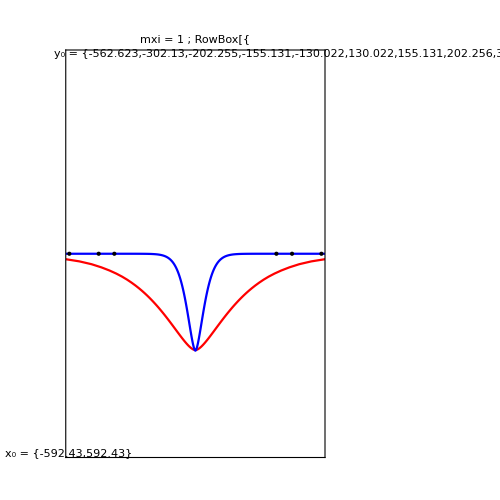
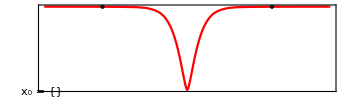
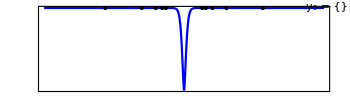
<|mainout→-Graphics-,xpts→{-592.43,592.43},ypts→{-562.623,-302.13,-202.255,-155.131,-130.022,130.022,155.131,202.256,302.13,562.616},xplt→-Graphics-,yplt→-Graphics-|>

```mathematica
llpgrid1k[[1,1]]
```

#### Data made here (~ 2 hrs, not bad! And less than 60 MB) OK - each LLP takes about 12 seconds. Going to rerun and remove the Column@AbsoluteTiming@Block b/c it makes getting parts much more awkward.

*** Uhhhhh what? the “lppgrid1k” file is 907 KB but “llpgrid1k” is 907 MB!?!?! What? How? Why?
Now that I think about it, the 907 KB file is almost certainly borked. But 907 MB seems like way too much. Maybe because of all the errors? I tried fixing the PlotLabel inside Show[], so we’ll see if/how much that matters.

```mathematica
{llptime1k,llpgrid1k}=AbsoluteTiming@Table[
Block[
{
bounds=(pio2-0.01),
ns=500,
ef=allmx[[mxi,ni]]
},
Block[
{
xdata=Table[
{
10*Tan[s],
ef[10*Tan[s],1]
},
{s,-bounds,bounds,2*bounds/ns}],
ydata=Table[
{
10*Tan[s],
ef[1,10*Tan[s]]
},
{s,-bounds,bounds,2*bounds/ns}],
lppopts={Mesh->{{0}},MeshFunctions->{#2&},MeshStyle->Directive[Black,PointSize[Medium]],PlotRange->Full,PlotTheme->"Detailed",Axes->True,AxesOrigin->{0,0},FrameTicks->None,ImageSize->{350,100},AspectRatio->Full,PlotLegends->None},
xplt,yplt,xpts,ypts
},
xplt=ListLinePlot[
xdata,
Evaluate@FilterRules[{lppopts},Options[ListLinePlot]],
PlotStyle->Red,
Epilog->{
Inset[Framed[Style[
TraditionalForm@StringForm["x_0 = `1`",xpts=Chop@Sort@Cases[Normal@xplt,Point[{x_,y_}]->x,Infinity]],Black,14
],Background->LightRed,RoundingRadius->5],
Scaled@{0.01,0.01},Scaled@{0.01,0.01}
]
}
];
yplt=ListLinePlot[
ydata,
Evaluate@FilterRules[{lppopts},Options[ListLinePlot]],
PlotStyle->Blue,
Epilog->{
Inset[Framed[Style[
TraditionalForm@StringForm["y_0 = `1`",ypts=Chop@Sort@Cases[Normal@yplt,Point[{x_,y_}]->x,Infinity]],Black,14
],Background->LightBlue,RoundingRadius->5],
Scaled@{0.99,0.99},Scaled@{0.99,0.99}
]
}
];
<|
"mainout"->Show[
{xplt,yplt},
ImageSize->{500,500},
PlotRange->{{-200,200},{-0.04,0.04}},
PlotLabel->StandardForm@StringForm["mxi = `1` ; n = `2`",mxi,ni]
],
"xpts"->xpts,"ypts"->ypts,"xplt"->xplt,"yplt"->yplt
|>
]],
{mxi,37},
{ni,12}
];
LightOrange~bg~llptime1k
Export[dfd<>"d_37x12-llp-zeros-list-2.m",llpgrid1k];
bmb@ByteCount@llpgrid1k
```

6228.8

52.5952 MB

### OK - develop the LLP idea (here be the low-res data from the first run)

#### Check it

```mathematica
TableForm@MapIndexed[Show[#1[[1,2]],PlotLabel->None,ImageSize->{200,200},Prolog->{Inset[Framed[Style[tssf["`1`",{#2[[1]],#2[[2]]+3}],14,Black],Background->LightGray,RoundingRadius->5],Scaled@{0.01,0.3},Scaled@{0.01,0.3}]}(*/.{PlotLabel->None(*tssf["`1`",#2]*)}*)]&,lppgrid[[1;;8,;;10]],{2}]
```

The second index in the brace is wrong but I can’t change it b/c I already took notes on it.

-Graphics-

#### Data made here (took like 45 min)

```mathematica
{lpptime,lppgrid}=AbsoluteTiming@Table[
Column@AbsoluteTiming@Block[
{
bounds=(pio2-0.05),
ns=200,
ef=allmx[[mxi,ni]]
},
Block[
{
xdata=Table[
{
10*Tan[s],
ef[10*Tan[s],1]
},
{s,-bounds,bounds,2*bounds/ns}],
ydata=Table[
{
10*Tan[s],
ef[1,10*Tan[s]]
},
{s,-bounds,bounds,2*bounds/ns}],
lppopts={Mesh->{{0}},MeshFunctions->{#2&},MeshStyle->Directive[Black,PointSize[Medium]],PlotRange->Full,PlotTheme->"Detailed",Axes->True,AxesOrigin->{0,0},FrameTicks->None,ImageSize->{350,100},AspectRatio->Full,PlotLegends->None},
xplt,yplt
},
xplt=ListLinePlot[
xdata,
Evaluate@FilterRules[{lppopts},Options[ListLinePlot]],
PlotStyle->Red
];
yplt=ListLinePlot[
ydata,
Evaluate@FilterRules[{lppopts},Options[ListLinePlot]],
PlotStyle->Blue
];
Show[
{xplt,yplt},
ImageSize->{500,500},
PlotRange->{{-200,200},{-0.04,0.04}},
PlotLabel->TraditionalForm@StringForm["mxi = `1` ; `2`",mxi,ni],
Epilog->{
Inset[Framed[Style[
TraditionalForm@StringForm["x_0 = `1`",Chop@Sort@Cases[Normal@xplt,Point[{x_,y_}]->x,Infinity]],Black,14
],Background->LightRed,RoundingRadius->5],
Scaled@{0.01,0.01},Scaled@{0.01,0.01}
],
Inset[Framed[Style[
TraditionalForm@StringForm["y_0 = `1`",Chop@Sort@Cases[Normal@yplt,Point[{x_,y_}]->x,Infinity]],Black,14
],Background->LightBlue,RoundingRadius->5],
Scaled@{0.99,0.99},Scaled@{0.99,0.99}
]
}
]]],
{mxi,37},
{ni,12}
];
LightOrange~bg~lpptime
```

2533.9

```mathematica
Export[dfd<>"d_37x12-lpp-zeros-list.m",lppgrid];
```

```mathematica
bmb@ByteCount@lppgrid
```

13.4602 MB

### Getting the zero’s from Plot[]?!?!?!?! EUUUHHHHHWHAAAAAAA? Uhhhh.... this is like exactly what I need. It’s not very precise but I just need to reliably count the zero’s along each axis.

#### Basic

```mathematica
Plot[
allmx[[1,6]][0,y],
{y,-100,100},
Mesh->{{0}},MeshFunctions->{#2&},MeshStyle->Directive[Black,PointSize[Medium]],PlotRange->All
]
Sort@Cases[Normal@%,Point[{x_,y_}]->x,Infinity]
```

#### Slightly Fancy

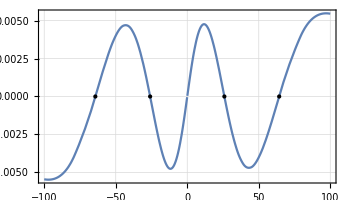
11.5178
{-64.2621,-25.9556,25.9562,64.2757}
-Graphics-

```mathematica
Column[
Flatten[AbsoluteTiming[Reverse@{
plt=Plot[
allmx[[1,6]][1,y],
{y,-100,100},
Mesh->{{0}},MeshFunctions->{#2&},MeshStyle->Directive[Black,PointSize[Medium]],PlotRange->All,
PlotTheme->"Detailed",Axes->True,AxesOrigin->{0,0},(*AxesStyle->Thick,*)FrameTicks->None,
ImageSize->{350,200},AspectRatio->Full,PlotLegends->None
],
Sort@Cases[Normal@plt,Point[{x_,y_}]->x,Infinity]
}],1],
Center
]
```

#### Show for x and y on one plot?? No good --- the mesh doesn’t specify which function corresponds to the mesh point at zero.

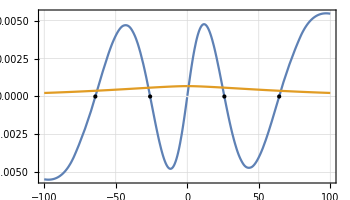
14.0554
{-64.2621,-25.9556,25.9562,64.2757}
-Graphics-

```mathematica
Column[
Flatten[AbsoluteTiming[Reverse@{
plt=Plot[
{
allmx[[1,6]][1,y],
allmx[[1,6]][y,1]
},
{y,-100,100},
Mesh->{{0}},MeshFunctions->{#2&},MeshStyle->Directive[Black,PointSize[Medium]],PlotRange->All,
PlotTheme->"Detailed",Axes->True,AxesOrigin->{0,0},(*AxesStyle->Thick,*)FrameTicks->None,
ImageSize->{350,200},AspectRatio->Full,PlotLegends->None
],
Sort@Cases[Normal@plt,Point[{x_,y_}]->x,Infinity]
}],1],
Center
]
```

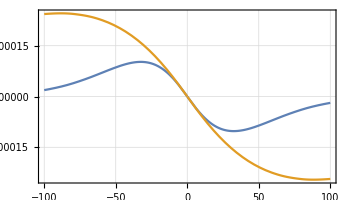
11.073
{}
-Graphics-

```mathematica
Column[
Flatten[AbsoluteTiming[Reverse@{
plt=Plot[
{
allmx[[2,10]][1,y],
allmx[[2,10]][y,1]
},
{y,-100,100},
Mesh->{{0}},MeshFunctions->{#2&},MeshStyle->Directive[Black,PointSize[Medium]],PlotRange->All,
PlotTheme->"Detailed",Axes->True,AxesOrigin->{0,0},(*AxesStyle->Thick,*)FrameTicks->None,
ImageSize->{350,200},AspectRatio->Full,PlotLegends->None
],
Sort@Cases[Normal@plt,Point[{x_,y_}]->x,Infinity]
}],1],
Center
]
```

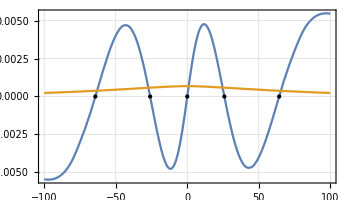
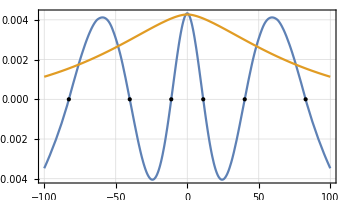
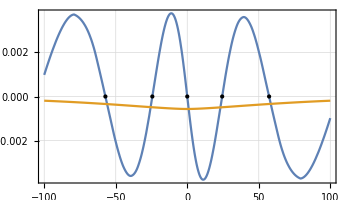
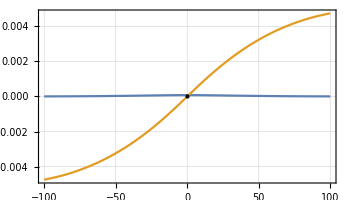
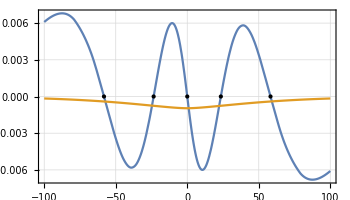
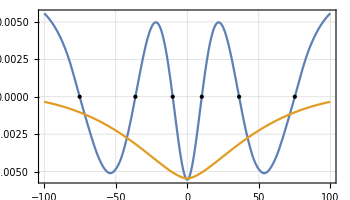
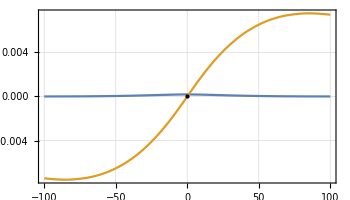
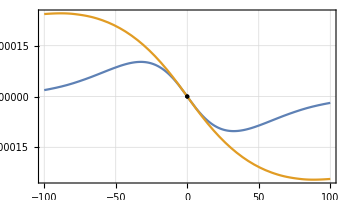
{252.183,13.8893
{-64.2621,-25.9556,-5.48348×10^-7,25.9562,64.2757}
-Graphics- | 12.6255
{-82.7829,-40.1948,-11.1867,11.1777,40.1905,82.7672}
-Graphics- | 13.8896
{-57.2265,-24.4141,-5.92728×10^-7,24.4182,57.228}
-Graphics- | 3.6573
{-0.0000799124}
-Graphics-
15.0389
{-58.2125,-23.4977,-7.785×10^-7,23.4886,58.212}
-Graphics- | 13.3574
{-75.2074,-36.257,-10.1674,10.1674,36.258,75.2126}
-Graphics- | 9.70566
{-0.000150388}
-Graphics- | 11.2264
{-0.000362875,-0.0000989068}
-Graphics-
11.2014
{-0.000217041}
-Graphics- | 14.9768
{-55.2502,-22.3271,-9.18051×10^-7,22.3281,55.2643}
-Graphics- | 13.6137
{-86.9035,-71.4007,-34.2675,-9.73207,9.73761,34.2691,71.4004,86.8854}
-Graphics- | 13.6979
{-90.9292,-49.342,-21.0918,-9.7363×10^-7,21.0871,49.3405,90.9288}
-Graphics-
12.1388
{-0.000280901}
-Graphics- | 13.7798
{-53.4568,-21.625,-1.01567×10^-6,21.622,53.4467}
-Graphics- | 11.9377
{-0.000636092,-0.000264581}
-Graphics- | 13.6075
{-87.8285,-47.6965,-20.4199,-2.36983×10^-6,20.4198,47.6987,87.8384}
-Graphics-
15.134
{-66.7015,-36.3262,-9.63261,9.64057,36.327,66.7246}
-Graphics- | 13.3199
{-52.1831,-21.1449,-1.09048×10^-6,21.1397,52.1807}
-Graphics- | 12.5788
{-0.000726151,-0.000318939}
-Graphics- | 12.7987
{-22.3419,-0.000347295,22.3317}
-Graphics-}

```mathematica
AbsoluteTiming@TableForm@Table[
Block[{
ef=allmx[[mxi,ni]]
},
Block[
{
plt=AbsoluteTiming@Plot[
{
ef[1,y],
ef[y,1]
},
{y,-100,100},
Mesh->{{0}},MeshFunctions->{#2&},MeshStyle->Directive[Black,PointSize[Medium]],PlotRange->All,
PlotTheme->"Detailed",Axes->True,AxesOrigin->{0,0},(*AxesStyle->Thick,*)FrameTicks->None,
ImageSize->{350,200},AspectRatio->Full,PlotLegends->None
]
},
framegrid[{{plt[[1]]},{Sort@Cases[Normal@plt,Point[{x_,y_}]->x,Infinity]},{plt[[2]]}}]
]
],
{mxi,1,5},
{ni,{6,7,8,10}}
]
```

#### Do we need to make two plots?? Yes, unfortunately. Eh. Plotting is sloooooowwwww... 20x6 table of 2 plots each took 1899 sec (31+ minutes!)

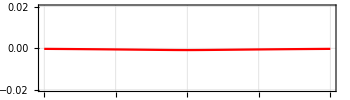
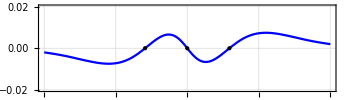
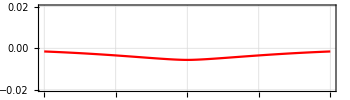
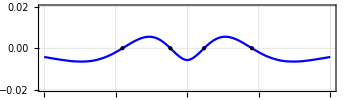
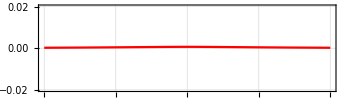
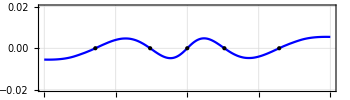
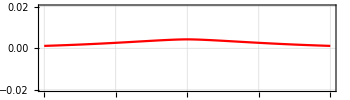
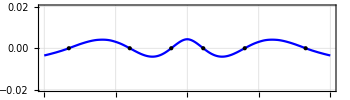
1899.85
2.82279 | 9.34499
{} | -Graphics-
{-29.4858,-4.77182×10^-7,29.4833} | -Graphics- | 3.09159 | 11.2769
{} | -Graphics-
{-45.2639,-11.7866,11.7849,45.2615} | -Graphics- | 2.65498 | 11.661
{} | -Graphics-
{-64.2621,-25.9556,-5.48348×10^-7,25.9562,64.2757} | -Graphics- | 2.73313 | 10.5896
{} | -Graphics-
{-82.7829,-40.1948,-11.1867,11.1777,40.1905,82.7672} | -Graphics- | 2.95717 | 11.9975
{} | -Graphics-
{-57.2265,-24.4141,-5.92728×10^-7,24.4182,57.228} | -Graphics- | 1.0811 | 2.9089
{-0.0000799124} | -Graphics-
{} | -Graphics-
2.8074 | 8.99006
{} | -Graphics-
{-26.62,-6.92871×10^-7,26.6179} | -Graphics- | 2.84033 | 10.9293
{} | -Graphics-
{-40.8441,-10.6741,10.6646,40.8379} | -Graphics- | 2.69508 | 12.9732
{} | -Graphics-
{-58.2125,-23.4977,-7.785×10^-7,23.4886,58.212} | -Graphics- | 2.98366 | 11.6278
{} | -Graphics-
{-75.2074,-36.257,-10.1674,10.1674,36.258,75.2126} | -Graphics- | 5.68931 | 3.98133
{-0.000150388} | -Graphics-
{} | -Graphics- | 5.61177 | 5.83718
{-0.0000989068} | -Graphics-
{-0.000362875} | -Graphics-
2.71673 | 9.13621
{} | -Graphics-
{-25.2794,-8.23544×10^-7,25.282} | -Graphics- | 2.64742 | 10.1032
{} | -Graphics-
{-38.664,-10.1451,10.1452,38.6643} | -Graphics- | 6.04879 | 5.38105
{-0.000217041} | -Graphics-
{} | -Graphics- | 2.50092 | 12.8053
{} | -Graphics-
{-55.2502,-22.3271,-9.18051×10^-7,22.3281,55.2643} | -Graphics- | 2.54902 | 11.5712
{-86.9035,86.8854} | -Graphics-
{-71.4007,-34.2675,-9.73207,9.73761,34.2691,71.4004} | -Graphics- | 2.57265 | 11.5937
{} | -Graphics-
{-90.9292,-49.342,-21.0918,-9.7363×10^-7,21.0871,49.3405,90.9288} | -Graphics-
2.56387 | 9.08589
{} | -Graphics-
{-24.45,-9.16556×10^-7,24.4548} | -Graphics- | 3.6817 | 10.2185
{-79.9129,79.9031} | -Graphics-
{-37.3095,-9.83622,9.83988,37.3083} | -Graphics- | 5.92408 | 6.64848
{-0.000280901} | -Graphics-
{} | -Graphics- | 3.06905 | 12.6872
{} | -Graphics-
{-53.4568,-21.625,-1.01567×10^-6,21.622,53.4467} | -Graphics- | 6.2379 | 6.00767
{-0.000264581} | -Graphics-
{-0.000636092} | -Graphics- | 2.47896 | 11.3979
{} | -Graphics-
{-87.8285,-47.6965,-20.4199,-2.36983×10^-6,20.4198,47.6987,87.8384} | -Graphics-
2.5103 | 9.18189
{} | -Graphics-
{-23.8613,-9.8828×10^-7,23.8682} | -Graphics- | 6.21089 | 6.73654
{-0.000342434} | -Graphics-
{} | -Graphics- | 5.45434 | 10.5222
{-66.7015,66.7246} | -Graphics-
{-36.3262,-9.63261,9.64057,36.327} | -Graphics- | 2.6929 | 11.008
{} | -Graphics-
{-52.1831,-21.1449,-1.09048×10^-6,21.1397,52.1807} | -Graphics- | 6.70399 | 6.17583
{-0.000318939} | -Graphics-
{-0.000726151} | -Graphics- | 5.98629 | 7.34191
{-0.000347295} | -Graphics-
{-22.3419,22.3317} | -Graphics-
3.29678 | 9.82771
{} | -Graphics-
{-23.3884,-1.04581×10^-6,23.3789} | -Graphics- | 6.22914 | 7.16323
{-0.000402079} | -Graphics-
{} | -Graphics- | 7.58538 | 9.91165
{-57.4107,57.4281} | -Graphics-
{-35.5426,-9.49375,9.49698,35.547} | -Graphics- | 3.49887 | 11.698
{} | -Graphics-
{-51.1919,-20.7503,-1.15171×10^-6,20.7481,51.1993} | -Graphics- | 5.95312 | 6.85986
{-0.000370929} | -Graphics-
{-0.000805651} | -Graphics- | 5.80023 | 6.79621
{-0.000431757} | -Graphics-
{-21.4352,21.4228} | -Graphics-
3.65858 | 9.49696
{} | -Graphics-
{-23.0366,-1.09385×10^-6,23.0292} | -Graphics- | 5.99455 | 7.39418
{-0.000460064} | -Graphics-
{} | -Graphics- | 8.3296 | 9.7237
{-50.4034,50.4207} | -Graphics-
{-34.8732,-9.3986,9.4016,34.8864} | -Graphics- | 5.84409 | 6.93506
{-0.000420849} | -Graphics-
{-0.000876821} | -Graphics- | 4.5234 | 11.6901
{-96.3841,96.3798} | -Graphics-
{-50.4057,-20.4631,-1.20164×10^-6,20.4631,50.4062} | -Graphics- | 5.8794 | 7.13742
{-0.000473322} | -Graphics-
{-20.6648,20.6683} | -Graphics-
4.66641 | 9.33046
{} | -Graphics-
{-22.7479,-1.13489×10^-6,22.7449} | -Graphics- | 5.93566 | 7.58787
{-0.000516599} | -Graphics-
{} | -Graphics- | 8.1569 | 9.55989
{-44.8927,44.8818} | -Graphics-
{-34.3097,-9.33713,9.33998,34.3101} | -Graphics- | 6.06074 | 7.12535
{-0.000468771} | -Graphics-
{-0.000941282} | -Graphics- | 4.79122 | 11.8719
{-87.0096,87.0163} | -Graphics-
{-49.755,-20.2395,-1.24373×10^-6,20.2381,49.7535} | -Graphics- | 5.7846 | 6.94838
{-0.000525212} | -Graphics-
{-20.1222,20.1144} | -Graphics-
5.66464 | 7.44632
{-0.000571838} | -Graphics-
{} | -Graphics- | 5.08325 | 9.16912
{-98.3558,98.3474} | -Graphics-
{-22.5095,-1.17005×10^-6,22.5084} | -Graphics- | 7.88687 | 9.7513
{-40.4318,40.4085} | -Graphics-
{-33.8062,-9.30427,9.30709,33.8051} | -Graphics- | 5.69168 | 7.43125
{-0.000514995} | -Graphics-
{-0.00100022} | -Graphics- | 5.83054 | 12.055
{-79.5041,79.5095} | -Graphics-
{-49.1979,-20.0588,-1.28025×10^-6,20.0552,49.1958} | -Graphics- | 5.51017 | 7.35436
{-0.000584222} | -Graphics-
{-19.6942,19.6747} | -Graphics-
5.4784 | 7.67458
{-0.000625908} | -Graphics-
{} | -Graphics- | 5.83797 | 9.2561
{-91.1947,91.2042} | -Graphics-
{-22.3123,-1.2012×10^-6,22.3098} | -Graphics- | 7.60357 | 9.67549
{-36.6704,36.6626} | -Graphics-
{-33.3333,-9.29806,9.30104,33.3316} | -Graphics- | 5.84683 | 7.513
{-0.000559689} | -Graphics-
{-0.00105452} | -Graphics- | 7.76579 | 11.6011
{-73.3344,73.3361} | -Graphics-
{-48.708,-19.9108,-1.31264×10^-6,19.9048,48.7063} | -Graphics- | 5.36254 | 7.56066
{-0.000641285} | -Graphics-
{-19.3433,19.3186} | -Graphics-
5.66237 | 8.01404
{-0.000678912} | -Graphics-
{} | -Graphics- | 6.10341 | 9.4468
{-85.2185,85.2245} | -Graphics-
{-22.144,-1.22859×10^-6,22.1408} | -Graphics- | 7.70676 | 9.88058
{-33.4653,33.4609} | -Graphics-
{-32.8693,-9.31901,9.32238,32.8677} | -Graphics- | 5.51704 | 7.60925
{-0.000602917} | -Graphics-
{-0.00110479} | -Graphics- | 8.45098 | 12.2778
{-67.989,67.9813} | -Graphics-
{-48.2674,-19.7892,-1.33099×10^-6,19.7806,48.2669} | -Graphics- | 6.35956 | 7.76628
{-0.000697673} | -Graphics-
{-19.0519,19.0275} | -Graphics-
5.66555 | 8.1276
{-0.000730939} | -Graphics-
{} | -Graphics- | 7.42856 | 9.62249
{-80.0516,80.0419} | -Graphics-
{-21.9985,-1.25347×10^-6,21.9947} | -Graphics- | 7.58471 | 10.5658
{-30.6623,30.6623} | -Graphics-
{-32.3926,-9.37002,9.37409,32.3916} | -Graphics- | 7.15162 | 8.25106
{-0.000645122} | -Graphics-
{-0.00115187} | -Graphics- | 7.57406 | 11.4942
{-14.8877,14.8895} | -Graphics-
{-54.3753,54.3818} | -Graphics- | 5.70683 | 7.53012
{-92.4348,-0.000753276,92.4143} | -Graphics-
{-18.8081,18.7882} | -Graphics-
6.29209 | 8.59967
{-0.00078206} | -Graphics-
{} | -Graphics- | 9.91261 | 10.3265
{-75.5835,75.5834} | -Graphics-
{-21.8713,-1.27566×10^-6,21.8671} | -Graphics- | 6.08641 | 8.41176
{-0.000686319} | -Graphics-
{-0.00119609} | -Graphics- | 7.73748 | 10.8324
{-28.2001,28.1845} | -Graphics-
{-31.8785,-9.45679,9.46198,31.8788} | -Graphics- | 8.05584 | 12.8822
{-13.5045,13.4962} | -Graphics-
{-51.9484,51.9285} | -Graphics- | 7.43663 | 8.19583
{-85.6434,-0.000808287,85.6504} | -Graphics-
{-18.6033,18.5899} | -Graphics-
6.1598 | 9.50886
{-0.000832342} | -Graphics-
{} | -Graphics- | 10.2757 | 10.6755
{-71.6462,71.6402} | -Graphics-
{-21.7594,-1.29594×10^-6,21.7546} | -Graphics- | 6.68021 | 9.19533
{-0.000725722} | -Graphics-
{-0.00123698} | -Graphics- | 8.59868 | 11.2814
{-25.9383,25.9437} | -Graphics-
{-31.2951,-9.58872,9.59562,31.2975} | -Graphics- | 8.34945 | 12.0948
{-12.1219,12.0683} | -Graphics-
{-49.4486,49.4438} | -Graphics- | 9.88569 | 13.2771
{-55.8588,55.8495} | -Graphics-
{-47.1275,-19.544,-1.41963×10^-6,19.528,47.1329} | -Graphics-
5.78786 | 9.21714
{-0.000881839} | -Graphics-
{} | -Graphics- | 10.1552 | 10.468
{-68.1574,68.1516} | -Graphics-
{-21.6601,-1.3145×10^-6,21.6549} | -Graphics- | 5.95778 | 8.92187
{-0.000764601} | -Graphics-
{-0.00127597} | -Graphics- | 7.84314 | 10.8945
{-23.9158,23.8995} | -Graphics-
{-30.6042,-9.78312,9.78966,30.6039} | -Graphics- | 8.08781 | 11.1646
{-10.51,10.5184} | -Graphics-
{-46.9652,46.9652} | -Graphics- | 8.79134 | 13.3381
{-52.659,52.6638} | -Graphics-
{-46.7967,-19.4955,-1.42907×10^-6,19.478,46.7939} | -Graphics-
6.0506 | 9.25357
{-0.000930601} | -Graphics-
{} | -Graphics- | 11.5249 | 11.6678
{-65.042,65.0443} | -Graphics-
{-21.5716,-1.33151×10^-6,21.5659} | -Graphics- | 6.5211 | 9.11824
{-0.000802507} | -Graphics-
{-0.00131281} | -Graphics- | 8.10125 | 10.8331
{-22.0149,22.0295} | -Graphics-
{-29.7625,-10.0655,10.0654,29.7581} | -Graphics- | 7.80444 | 10.9208
{-8.36897,8.36178} | -Graphics-
{-44.6586,44.6461} | -Graphics- | 9.31099 | 13.7467
{-49.7857,49.776} | -Graphics-
{-46.4779,-19.4621,-1.44336×10^-6,19.4438,46.4736} | -Graphics-
7.18081 | 9.89424
{-0.00097867} | -Graphics-
{} | -Graphics- | 10.2624 | 11.3779
{-62.2609,62.2671} | -Graphics-
{-21.4923,-1.34723×10^-6,21.4862} | -Graphics- | 6.01396 | 9.10816
{-0.000839552} | -Graphics-
{-0.00134775} | -Graphics- | 7.67733 | 11.3465
{-20.2994,20.295} | -Graphics-
{-28.6781,-10.4856,10.4763,28.6779} | -Graphics- | 7.9795 | 10.5905
{-4.3751,4.37728} | -Graphics-
{-42.5016,42.507} | -Graphics- | 8.83511 | 11.7822
{-47.0946,47.0944} | -Graphics-
{-46.1621,-19.4442,-1.45798×10^-6,19.425,46.1568} | -Graphics-
5.63842 | 8.1447
{-0.00102609} | -Graphics-
{} | -Graphics- | 7.97137 | 9.00807
{-59.748,59.7369} | -Graphics-
{-21.421,-1.36187×10^-6,21.4146} | -Graphics- | 4.9265 | 7.80774
{-0.000875793} | -Graphics-
{-0.00138097} | -Graphics- | 8.27786 | 10.9523
{-18.7483,18.7336} | -Graphics-
{-27.2392,-11.0777,11.0732,27.2523} | -Graphics- | 7.9807 | 10.5687
{} | -Graphics-
{-40.6065,-3.43454,3.43345,40.5876} | -Graphics- | 8.60198 | 12.3982
{-44.6318,44.6371} | -Graphics-
{-45.8421,-19.4428,-1.47108×10^-6,19.4225,45.8361} | -Graphics-
6.65986 | 9.42313
{-0.00107289} | -Graphics-
{} | -Graphics- | 9.344 | 10.3425
{-57.4273,57.4173} | -Graphics-
{-21.3567,-1.37531×10^-6,21.3499} | -Graphics- | 6.03254 | 8.97191
{-0.000911274} | -Graphics-
{-0.00141263} | -Graphics- | 7.82388 | 10.8294
{-17.4083,17.4154} | -Graphics-
{-25.345,-11.9531,11.9585,25.3213} | -Graphics- | 8.50813 | 10.724
{} | -Graphics-
{-39.009,-4.83615,4.83251,39.0018} | -Graphics- | 8.80285 | 12.3991
{-42.3265,42.3328} | -Graphics-
{-45.5091,-19.4596,-1.48318×10^-6,19.4383,45.5028} | -Graphics-
6.9686 | 9.75421
{-0.0011191} | -Graphics-
{} | -Graphics- | 9.53566 | 10.3834
{-55.3051,55.2996} | -Graphics-
{-21.2986,-1.38793×10^-6,21.2915} | -Graphics- | 5.93306 | 8.61966
{-0.000946044} | -Graphics-
{-0.00144286} | -Graphics- | 7.50083 | 10.9017
{-16.1781,16.2462} | -Graphics-
{-22.7229,-13.3668,13.3598,22.7281} | -Graphics- | 9.66495 | 10.4639
{} | -Graphics-
{-37.7437,-5.65804,5.6496,37.7613} | -Graphics- | 7.51509 | 11.287
{-40.1252,40.1336} | -Graphics-
{-45.1528,-19.4981,-1.49336×10^-6,19.4755,45.1465} | -Graphics-

```mathematica
Column@AbsoluteTiming@TableForm@Table[
Block[{
ef=allmx[[mxi,ni]]
},
Block[
{
pltx=AbsoluteTiming@Plot[
ef[x,1],
{x,-100,100},
Mesh->{{0}},MeshFunctions->{#2&},MeshStyle->Directive[Black,PointSize[Medium]],PlotRange->{{-100,100},{-0.02,0.02}},
PlotTheme->"Detailed",PlotStyle->Red,
Axes->True,AxesOrigin->{0,0},(*AxesStyle->Thick,*)FrameTicks->None,
ImageSize->{350,100},AspectRatio->Full,PlotLegends->None
],
plty=AbsoluteTiming@Plot[
ef[1,y],
{y,-100,100},
Mesh->{{0}},MeshFunctions->{#2&},MeshStyle->Directive[Black,PointSize[Medium]],PlotRange->{{-100,100},{-0.02,0.02}},
PlotTheme->"Detailed",PlotStyle->Blue,
Axes->True,AxesOrigin->{0,0},(*AxesStyle->Thick,*)FrameTicks->None,
ImageSize->{350,100},AspectRatio->Full,PlotLegends->None
]
},
framegrid[
{
{pltx[[1]],plty[[1]]},
{Sort@Cases[Normal@pltx,Point[{x_,y_}]->x,Infinity],pltx[[2]]},
{Sort@Cases[Normal@plty,Point[{x_,y_}]->x,Infinity],plty[[2]]}
}
]
]
],
{mxi,20},
{ni,{4,5,6,7,8,10}}
]
```

#### Can I sorta fudge it using ListLinePlot and a sparse Table of points? Yes!

```mathematica
{lpptime,lppgrid}=AbsoluteTiming@Table[
Column@AbsoluteTiming@Block[
{
bounds=(pio2-0.05),
ns=200,
ef=allmx[[mxi,ni]]
},
Block[
{
xdata=Table[
{
10*Tan[s],
ef[10*Tan[s],1]
},
{s,-bounds,bounds,2*bounds/ns}],
ydata=Table[
{
10*Tan[s],
ef[1,10*Tan[s]]
},
{s,-bounds,bounds,2*bounds/ns}],
lppopts={Mesh->{{0}},MeshFunctions->{#2&},MeshStyle->Directive[Black,PointSize[Medium]],PlotRange->Full,PlotTheme->"Detailed",Axes->True,AxesOrigin->{0,0},FrameTicks->None,ImageSize->{350,100},AspectRatio->Full,PlotLegends->None},
xplt,yplt
},
xplt=ListLinePlot[
xdata,
Evaluate@FilterRules[{lppopts},Options[ListLinePlot]],
PlotStyle->Red
];
yplt=ListLinePlot[
ydata,
Evaluate@FilterRules[{lppopts},Options[ListLinePlot]],
PlotStyle->Blue
];
Show[
{xplt,yplt},
ImageSize->{500,500},
PlotRange->{{-200,200},{-0.04,0.04}},
PlotLabel->TraditionalForm@StringForm["mxi = `1` ; `2`",mxi,ni],
Epilog->{
Inset[Framed[Style[
TraditionalForm@StringForm["x_0 = `1`",Chop@Sort@Cases[Normal@xplt,Point[{x_,y_}]->x,Infinity]],Black,14
],Background->LightRed,RoundingRadius->5],
Scaled@{0.01,0.01},Scaled@{0.01,0.01}
],
Inset[Framed[Style[
TraditionalForm@StringForm["y_0 = `1`",Chop@Sort@Cases[Normal@yplt,Point[{x_,y_}]->x,Infinity]],Black,14
],Background->LightBlue,RoundingRadius->5],
Scaled@{0.99,0.99},Scaled@{0.99,0.99}
]
}
]]],
{mxi,37},
{ni,12}
];
LightOrange~bg~lpptime
```

2533.9

```mathematica
Export[dfd<>"d_37x12-lpp-zeros-list.m",lppgrid];
```

```mathematica
bmb@ByteCount@lppgrid
```

13.4602 MB

```mathematica
Import[dfd<>"d_37x12-lpp-zeros-list.m"]
```

Syntax::sntue: Unexpected end of file (probably unfinished expression)  (line 13884 of "/home/matt/datadrop/Dropbox/Berman-Research/dis/figs/d_37x12-lpp-zeros-list.m").

# Wacky idea: turn RK into Coulomb with a coordinate transform (probs wont work)

```mathematica
D[-(1/r)+(StruveH[0,a r]-BesselY[0,a r]),r][0]
```

(1/r^2+a BesselY[1,a r]+1/2 a (2/π+StruveH[-1,a r]-StruveH[1,a r]))[0]

```mathematica
Manipulate[
Block[{plt=Plot[
{
-1/r,
-(StruveH[0,a r]-BesselY[0,a r]),
-(1/r)+(StruveH[0,a r]-BesselY[0,a r]),
D[-(1/rp)+(StruveH[0,a rp]-BesselY[0,a rp]),rp]/.rp->r
},
{r,0,(rmax*10^rmxn)},
Mesh->{{0}},MeshFunctions->{#2&},MeshStyle->Directive[Black,PointSize[Medium]],PlotRange->{{0,(rmax*10^rmxn)},{-(ymax*(10^ymxn)),(ymax*(10^ymxn))}},PlotTheme->"Detailed",Axes->True,ImageSize->0.8*{1600,1200},AspectRatio->3/4,PlotLegends->None
]
},
Show[plt,Epilog->{
Inset[Framed[Style[
TraditionalForm@StringForm["x_0 = `1`",Chop@Sort@Cases[Normal@plt,Point[{x_,y_}]->{x,y},Infinity]],Black,14
],Background->LightRed,RoundingRadius->5],
Scaled@{0.01,0.99},Scaled@{0.01,0.99}
]
}
]
],
Row[{Control@{a,0.031,1},Control@{rmax,1,10,1},Control@{{rmxn,2},2,9,1,ControlType->Setter},Control@{{ymax,3},1,10,1},Control@{{ymxn,0},{-6,-5,-4,-3,-2,-1,0}}},Spacer@20]
]
```